# Define functions and module for general ODE

```mathematica
(*ρi = 0.1;(*ratio of ice/rock density*)*)
bv = bmax*(x^2-1);(* quadratic basal topography*)
eqiceODE = (ρ-1)(D[H[x],x]+D[bv,x]) - 0.5*((α-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*α))*H[x]  -ρ*((Abs[b0]-b0) - H[x]-bv+ x*α)*(fλ/H[x]+D[bv,x,x]*(α/(1+D[bv,x]*α)-D[bv,x]/ (1+(D[bv,x])^2)))==fλ + ρ *α-(α-D[bv,x])/(1+D[bv,x]*α);
(*eqiceODE/.bmax->b0*)
(*define function to find landslide toe*)
xPosRoot[ρv_?NumericQ,αv_?NumericQ,fv_?NumericQ, b0_?NumericQ]:=Module[{sol,res},
xend=0.0;sol=Quiet@Check[NDSolve[{eqiceODE/.{ρ->ρv,bmax->b0,α->αv,fλ->fv},H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xend=x,"StopIntegration"}]},H,{x,0,1}],$Failed];
If[sol===$Failed,0.0,(*fallback if solve fails*)
res=xend
]
]
```

## Insert values for a test case

0.924747

0.924747

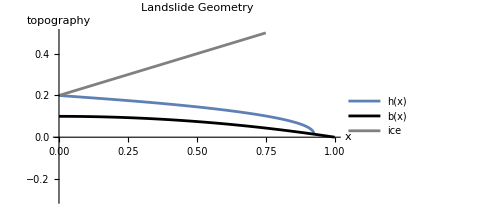

```mathematica
αv=0.4;
fv=0.45;
b0=-0.1;
ρi = 0.1;
xPosRoot[ρi,αv,fv,b0]
xendice=1.0;
solice = NDSolve[{eqiceODE/.{ρ->ρi,bmax->b0,α->αv,fλ->fv},H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
xendice
(*thickness has artifacts*)
Hsol= H[x]/.solice;
Hice[x_]:=Piecewise[{{Evaluate[Hsol],0<=x<=xendice }},0]
Plot[{Hice[x]+bv/.bmax->b0,bv/.bmax->b0,Abs[b0]-b0+x*αv},{x,0,1},PlotStyle->{DarkBlue,Black,Gray},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","b(x)","ice"},ImageSize->Medium,PlotRange->{-0.3,0.5}]
```

## Define locus function and plot stability criteria

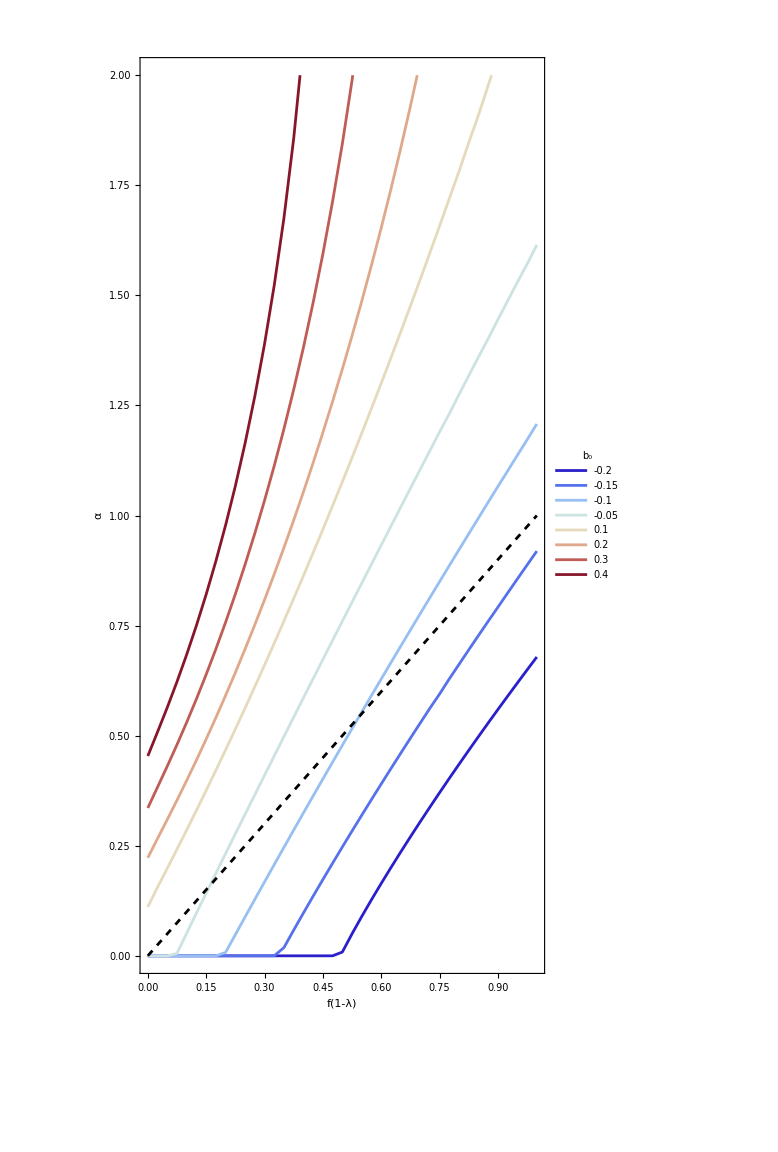

```mathematica
locusfun[ρ_,f_,b0_]:=Module[{res},res=
Quiet@FindRoot[xPosRoot[ρ,αsol,f,b0]==1.0,{αsol,0.0,0,10}];
αsol/. res]
bvals=Join[{-0.2,-0.15,-0.1,-0.05},Subdivide[0.1,0.4,3]];
roundedLabels = Round[bvals,0.01];
fvals=Range[0,1,0.025];  

(*Parallel computation of {f,alpha} pairs for each ρ,b value*)
ρvalue=0.1;
(*xPosRoot[ρvalue,0.6,0.6,bvals[[5]]]*)

data=ParallelTable[{f,locusfun[ρvalue,f,b]},{b,bvals},{f,fvals}];
(*Plot each set of points as a line*)
p1=ListLinePlot[data,PlotRange->{0,2},PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,20]],Right],
LabelStyle->{FontSize->20},
ImageSize->Large,PlotStyle->ColorData["ThermometerColors"]/@Rescale[Range[Length[bvals]]]];
p2=Plot[f,{f,0,1},PlotStyle->{Black,Dashed}];
fig=Show[p1,p2,FrameLabel->{"f(1-λ)","α"},Frame->True,LabelStyle->{FontSize->25},AspectRatio->2]
(*Export[NotebookDirectory[]<>"LandslideIceToeTrueStabilityBoundaryPlot_rho"<>ToString[ρvalue]<>".jpg",fig,"JPEG"]*)
```

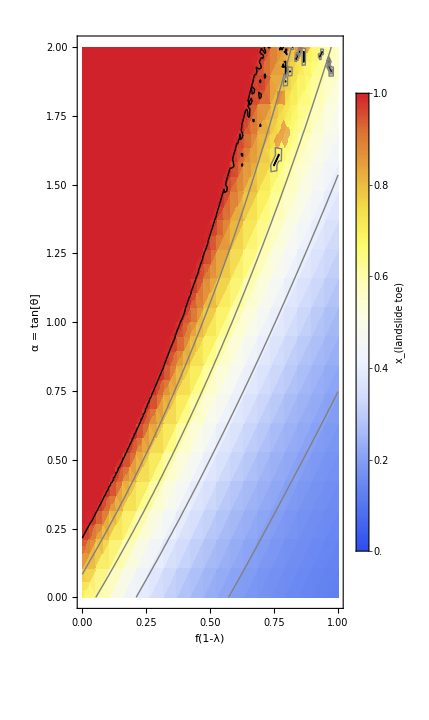

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeIceParameterPlot.jpg

```mathematica
(*define function to find landslide toe*)
ρvalue = 0.1;
xPosRoot[ρv_?NumericQ,αv_?NumericQ,fv_?NumericQ, b0_?NumericQ]:=Module[{sol,res},
xend=1.01;sol=Quiet@Check[NDSolve[{eqiceODE/.{ρ->ρv,bmax->b0,α->αv,fλ->fv},H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xend=x,"StopIntegration"}]},H,{x,0,1}],$Failed];
If[sol===$Failed,1.01,(*fallback if solve fails*)
res=xend
]
]
bplotval = 0.2;
contours={0,0.2,0.4,0.6,0.8,0.99};
dplot=DensityPlot[
Clip[xPosRoot[ρvalue,αv,fv,bplotval],{0,1.1}],(*clamp values to[0,1]*){fv,0,1},{αv,0,2},ColorFunction->(ColorData[{"Temperature",{0,1}}][#]&),ColorFunctionScaling->False,(*use actual values,not rescaled*)FrameLabel->{"f(1-λ)","α = tan[θ]"},PlotPoints->20,Mesh->False,PlotLegends->BarLegend[{ColorData[{"Temperature",{0,1}}],{0,1}},LegendLabel->Style[Subscript[x,"landslide toe"],FontSize->14]],ImageSize->Medium,LabelStyle->{FontSize->15}];

cplot=ContourPlot[xPosRoot[ρvalue,αv,fv,bplotval],{fv,0,1},{αv,0,2},Contours->contours,ContourStyle->{Gray,Gray,Gray,Gray,Gray,Directive[Black,Thick]},ContourShading->None];

fig=Show[dplot,cplot,AspectRatio->2]
Export[NotebookDirectory[]<>"LandslideToeIceParameterPlot.jpg",fig,"JPEG",ImageResolution->500]
```

## Plot profiles

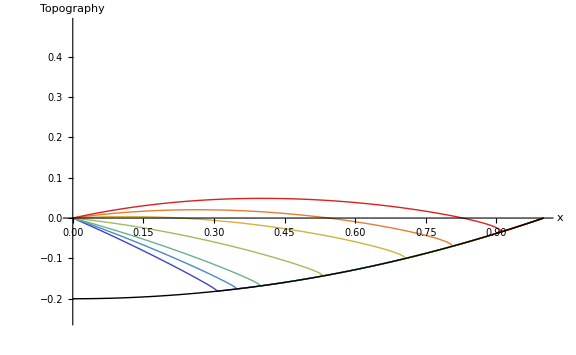

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeIceTopographicProfiles.jpg

```mathematica
fvval = 0.6;
bplotval = 0.2;
ρvalue = 0.01;
paramSets={
{0.1,fvval,bplotval},
{0.2,fvval,bplotval},
{0.3,fvval,bplotval},
{0.5,fvval,bplotval},
{0.7,fvval,bplotval},
{0.8,fvval,bplotval},
{0.9,fvval,bplotval}};
(*Number of parameter sets*)
nlines=Length[paramSets];
(*Hsol[αv_?NumericQ,fv_?NumericQ,b0_?NumericQ]:=
Quiet@Module[{bv,sol,H},
(*Define the profile bv[x] here if needed*)
bv[x_]:=b0*(x^2-1);
eqiceODE = (ρvalue-1)(D[H[x],x]+D[bv,x]) - 0.5*((αv-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*αv))*H[x]  -ρvalue*((Abs[b0]-b0) - H[x]-bv+ x*αv)*(fv/H[x]+D[bv,x,x]*(αv/(1+D[bv,x]*αv)-D[bv,x]/ (1+(D[bv,x])^2)))==fv + ρvalue *αv-(αv-D[bv,x])/(1+D[bv,x]*αv);
xendice=1.0;
sol = NDSolve[{eqiceODE,H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
(*thickness has artifacts*)
Hsol= H[x]/.sol;
Hice[x_]:=Piecewise[{{Evaluate[Hsol],0<=x<=xendice }},0];
Function[x,Hice]
];*)
Hsol[αv_?NumericQ,fv_?NumericQ,b0_?NumericQ]:=Quiet@Module[{bv,sol,xendice,Hfun},(*Define basal profile*)bv[x_]:=b0*(x^2-1);
(*Define ODE*)eqiceODE=(ρvalue-1) (H'[x]+D[bv[x],x])-0.5*((αv-D[bv[x],x])/(1+(D[bv[x],x])^2)*D[bv[x],{x,2}]/(1+D[bv[x],x]*αv)) H[x]-ρvalue*((Abs[b0]-b0)-H[x]-bv[x]+x*αv)*(fv/H[x]+D[bv[x],{x,2}]*(αv/(1+D[bv[x],x]*αv)-D[bv[x],x]/(1+(D[bv[x],x])^2)))==fv+ρvalue*αv-(αv-D[bv[x],x])/(1+D[bv[x],x]*αv);
xendice=1.0;
(*Solve ODE with stopping condition*)sol=NDSolve[{eqiceODE,H[0]==Abs[b0],WhenEvent[H[x]<=10^-3,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
(*Extract interpolating function*)
Hfun=First[H/. sol];
(*Define piecewise thickness function*)Function[x,Piecewise[{{Hfun[x],0<=x<=xendice}},0]]];
 
(*Generate a list of H[x]+b[x] and b[x] curves for each parameter set*)
curves = Table[Module[{Hf,αv,fv,b0,color},{αv,fv,b0}=
paramSets[[i]];
Hf=Hsol[αv,fv,b0];
color=ColorData["Rainbow"][i/nlines];(*gradient from blue to red*)
{Style[Hf[x]+bplotval*(x^2-1),color,Thick]}  (*dashed baseline*)],{i,nlines}];

(*Flatten the list so all curves are in a single list*)
curvesFlat=Flatten[curves,1];

(*Plot all curves together*)
fig=Plot[Evaluate[Join[curvesFlat,{Style[bplotval*(x^2-1),Black,Thick]}]],{x,0,1},
PlotRange->{-1.25*bplotval,2.4*bplotval},PlotLegends->None,Frame->None,AxesLabel->{"x","Topography"},LabelStyle->{FontSize->20},ImageSize->Large]
Export[NotebookDirectory[]<>"LandslideToeIceTopographicProfiles.jpg",fig,"JPEG",ImageResolution->500]
```